```mathematica
receipts=Import["http://www.whatwepayfor.com/api/getReceiptAccount?year=1999","XML"];
```

```mathematica
expenses=Import["http://www.whatwepayfor.com/api/getBudgetAccount?income=100&showChange=1&showExtra=1&year=1999","XML"];
```

```mathematica
accountPairs={#[[1]],ToExpression[#[[2]]]}&/@Cases[expenses,XMLElement["item",{___,"account"->ac_,___,"amounti"->am_,___},___]->{ac,am},Infinity];
```

```mathematica
NetAccountAmount[indexes_]:=Total[accountPairs[[indexes,2]]];
```

```mathematica
ToBaseWord[w_]:=Block[{wn},wn=WordData[w];If[Length[wn]≤0,w,wn[[1,1]]]];
```

```mathematica
MeaningQ[w_]:=Block[{wn},wn=WordData[w,"PartsOfSpeech"];
NumberQ[w]
||(Not[MemberQ[wn,"Preposition"]]
&&Not[MemberQ[wn,"Conjunction"]]
&&Not[MemberQ[wn,"Determiner"]]
)
];
```

```mathematica
YearPlot[year_]:=Block[{expenses,accountPairs,wordToAccountIds0,wordToAccountIds,sum,maxCount,maxAmount,sum2},

expenses=Import["http://www.whatwepayfor.com/api/getBudgetAccount?income=100&showChange=1&showExtra=1&year="<>ToString[year],"XML"];
accountPairs={#[[1]],ToExpression[#[[2]]]}&/@Cases[expenses,XMLElement["item",{___,"account"->ac_,___,"amounti"->am_,___},___]->{ac,am},Infinity];
wordToAccountIds0=Flatten[Function[{accountIndex},{ToBaseWord[ToLowerCase[#]],accountIndex}&/@StringSplit[accountPairs[[accountIndex,1]],RegularExpression["[^a-zA-Z0-9]+"]]]/@Range[1,Length[accountPairs]],1];
wordToAccountIds=Select[{#[[1,1]],#[[All,2]]}&/@GatherBy[wordToAccountIds0,#[[1]]&],
MeaningQ[#[[1]]]&];

sum={#[[1]],Length[Union[#[[2]]]],NetAccountAmount[Union[#[[2]]]]}&/@wordToAccountIds;
maxCount=Max[sum[[All,2]]];
maxAmount=Max[sum[[All,3]]];
sum2={#[[1]],#[[2]],#[[3]],N[#[[2]]/maxCount],N[#[[3]]/maxAmount]}&/@sum;
ListLinePlot[{SortBy[sum2,(-#[[2]])&][[1;;1000,4]],SortBy[sum2,(-#[[2]])&][[1;;1000,5]]},PlotRange->{All,{-0.3,1}},
AspectRatio->(1/6),ImageSize->{1600,Automatic}]
]
```

FetchURL::conopen: The connection to URL http://www.whatwepayfor.com/api/getBudgetAccount?income=100&showChange=1&showExtra=1&year=1980 cannot be opened. If the URL is correct, you might need to configure your firewall program, or you might need to set a proxy in the Internet connectivity tab of the Preferences dialog (or by calling SetInternetProxy).  For HTTPS connections, you might need to inspect the authenticity of the server's SSL certificate and choose to accept it.

Part::take: Cannot take positions 1 through 1000 in {}.

-Graphics-

FetchURL::conopen: The connection to URL http://www.whatwepayfor.com/api/getBudgetAccount?income=100&showChange=1&showExtra=1&year=1981 cannot be opened. If the URL is correct, you might need to configure your firewall program, or you might need to set a proxy in the Internet connectivity tab of the Preferences dialog (or by calling SetInternetProxy).  For HTTPS connections, you might need to inspect the authenticity of the server's SSL certificate and choose to accept it.

Part::take: Cannot take positions 1 through 1000 in {}.

-Graphics-

FetchURL::conopen: The connection to URL http://www.whatwepayfor.com/api/getBudgetAccount?income=100&showChange=1&showExtra=1&year=1982 cannot be opened. If the URL is correct, you might need to configure your firewall program, or you might need to set a proxy in the Internet connectivity tab of the Preferences dialog (or by calling SetInternetProxy).  For HTTPS connections, you might need to inspect the authenticity of the server's SSL certificate and choose to accept it.

Part::take: Cannot take positions 1 through 1000 in {}.

-Graphics-

FetchURL::conopen: The connection to URL http://www.whatwepayfor.com/api/getBudgetAccount?income=100&showChange=1&showExtra=1&year=1983 cannot be opened. If the URL is correct, you might need to configure your firewall program, or you might need to set a proxy in the Internet connectivity tab of the Preferences dialog (or by calling SetInternetProxy).  For HTTPS connections, you might need to inspect the authenticity of the server's SSL certificate and choose to accept it.

Part::take: Cannot take positions 1 through 1000 in {}.

-Graphics-

Part::take: Cannot take positions 1 through 1000 in {{.

General::stop: Further output of Part will be suppressed during this calculation.

-Graphics-

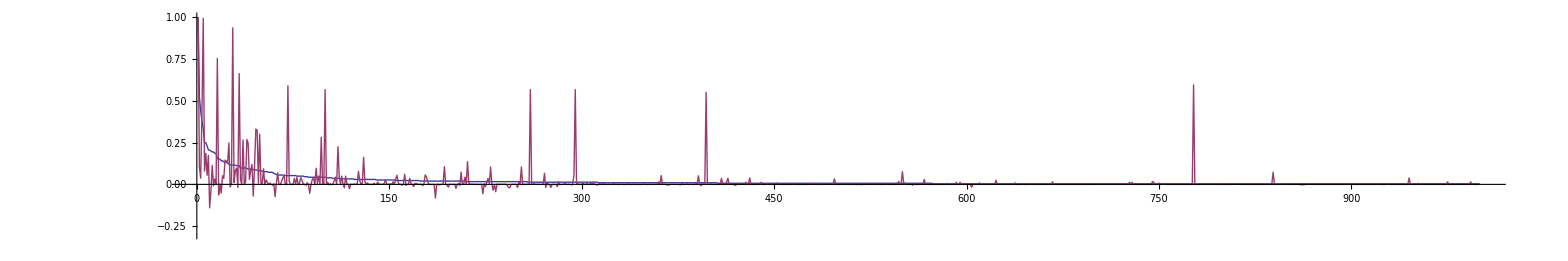

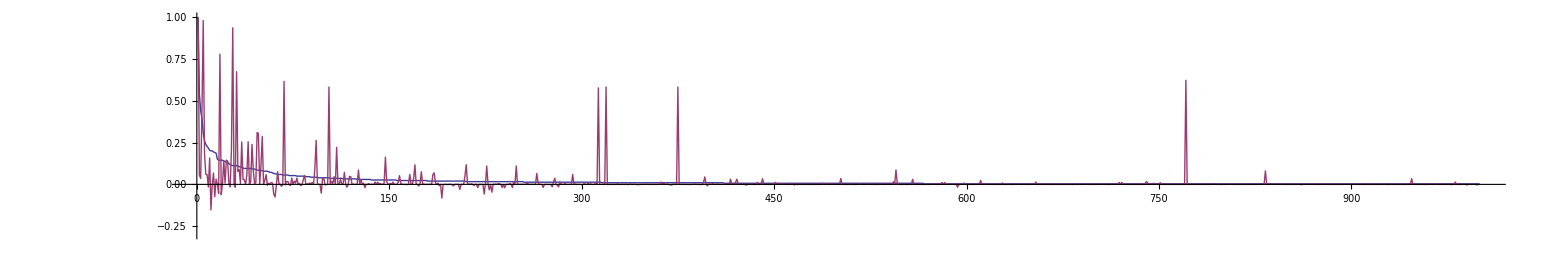

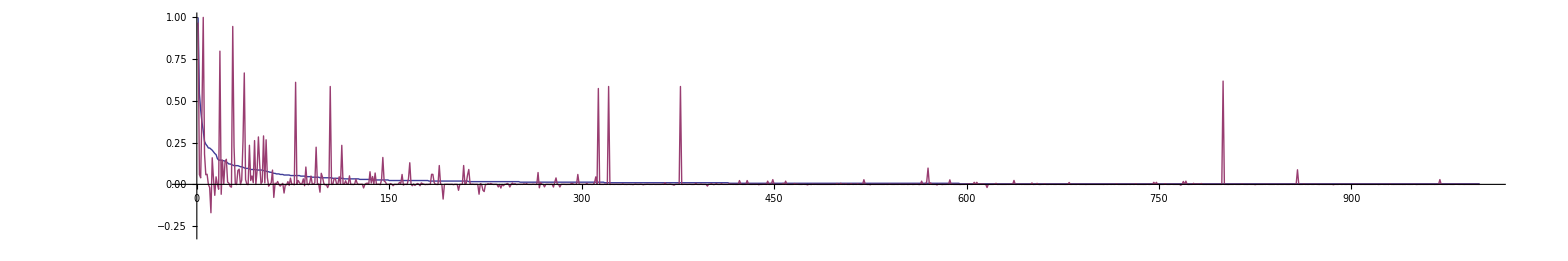

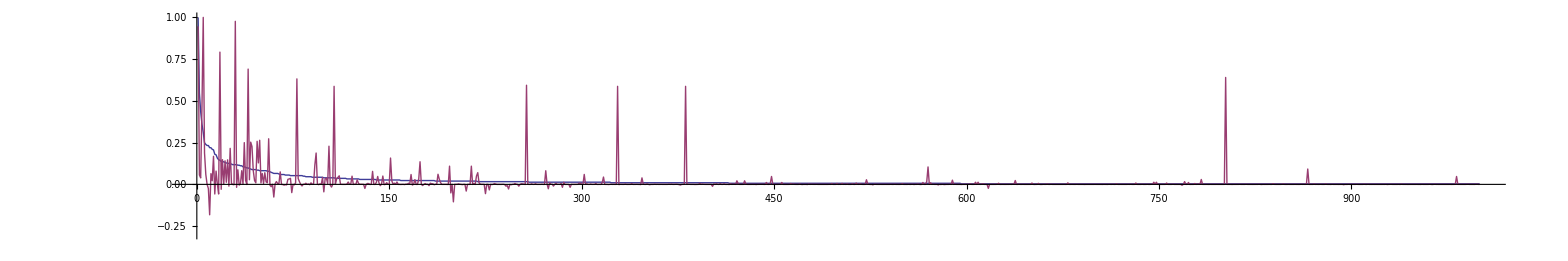

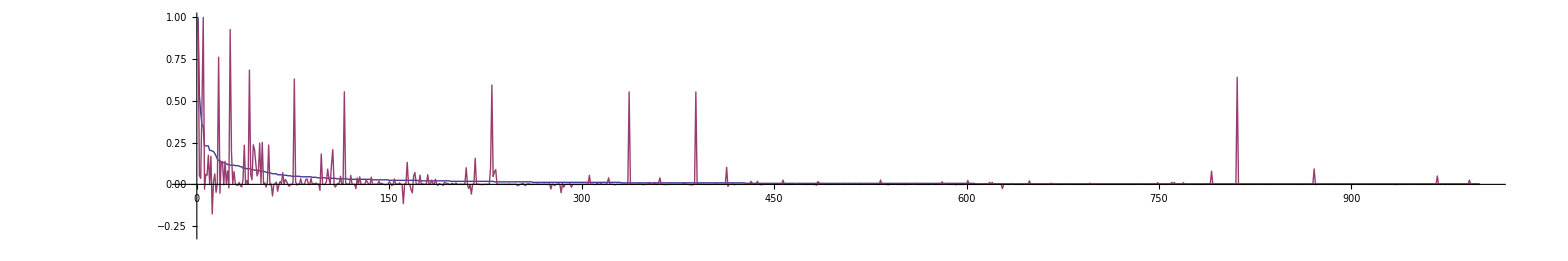

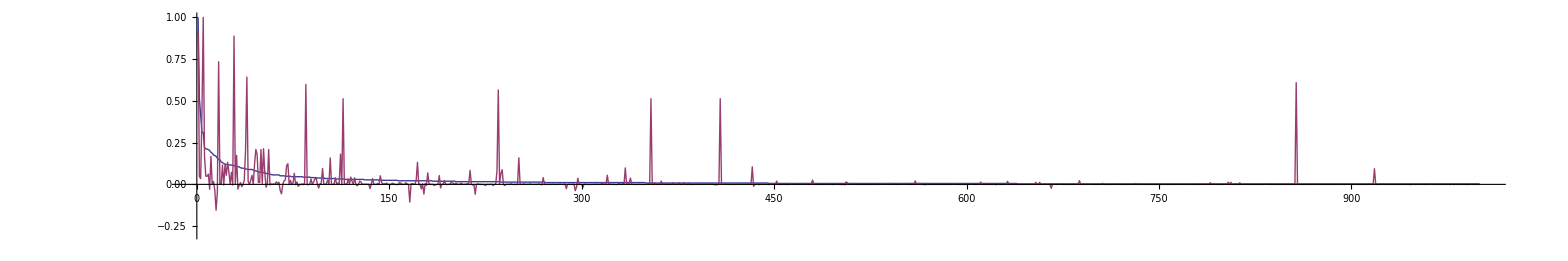

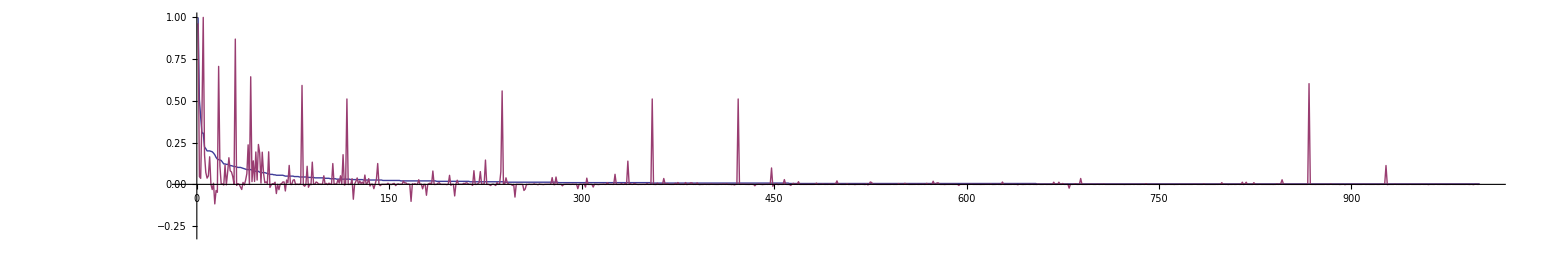

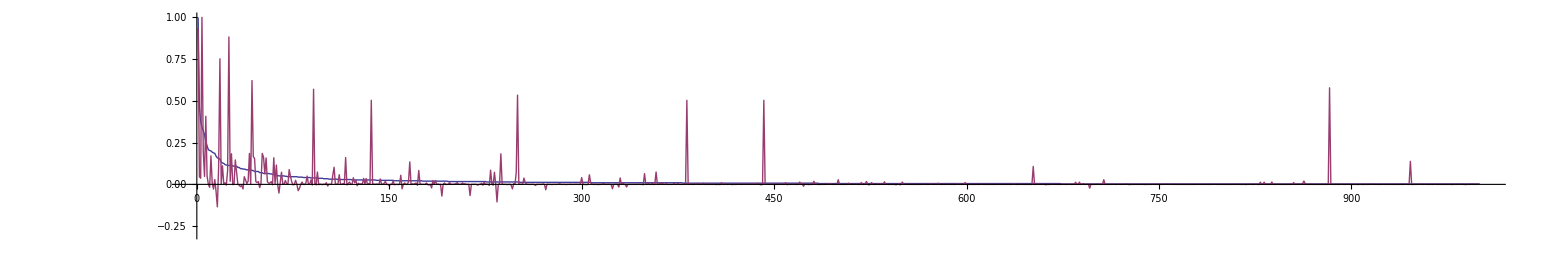

```mathematica
YearPlot[1980]
YearPlot[1981]
YearPlot[1982]
YearPlot[1983]
YearPlot[1984]
YearPlot[1985]
YearPlot[1986]
YearPlot[1987]
YearPlot[1988]
YearPlot[1989]
YearPlot[1990]
YearPlot[1991]
YearPlot[1992]
YearPlot[1993]
YearPlot[1994]
YearPlot[1995]
YearPlot[1996]
YearPlot[1997]
YearPlot[1998]
YearPlot[1999]
YearPlot[2000]
YearPlot[2001]
YearPlot[2002]
YearPlot[2003]
YearPlot[2004]
YearPlot[2005]
YearPlot[2006]
YearPlot[2007]
YearPlot[2008]
YearPlot[2009]
YearPlot[2010]
```